This notebook shows the Landau Levels in WSM implemented on a parent lattice

```mathematica
tStart=AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
(**Change the system size here **)
```

```mathematica
Lx=32;
Ly=32;
A=Lx*Ly;
```

```mathematica
B=1/Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(**-----------------Define the sine and cosine matrices for the parent square lattice--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define Hamiltonian **)
(** We will use mixed boundary conditions, PBC in x and OBC in y.Therefore, αx = 1 and αy = 0 **)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-2t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(** Generate a vector where values of kz for which we will diagonalize the Hamiltonian is stored **)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,100]
```

{-3.14159,-3.07876,-3.01593,-2.9531,-2.89027,-2.82743,-2.7646,-2.70177,-2.63894,-2.57611,-2.51327,-2.45044,-2.38761,-2.32478,-2.26195,-2.19911,-2.13628,-2.07345,-2.01062,-1.94779,-1.88496,-1.82212,-1.75929,-1.69646,-1.63363,-1.5708,-1.50796,-1.44513,-1.3823,-1.31947,-1.25664,-1.19381,-1.13097,-1.06814,-1.00531,-0.942478,-0.879646,-0.816814,-0.753982,-0.69115,-0.628319,-0.565487,-0.502655,-0.439823,-0.376991,-0.314159,-0.251327,-0.188496,-0.125664,-0.0628319,0.,0.0628319,0.125664,0.188496,0.251327,0.314159,0.376991,0.439823,0.502655,0.565487,0.628319,0.69115,0.753982,0.816814,0.879646,0.942478,1.00531,1.06814,1.13097,1.19381,1.25664,1.31947,1.3823,1.44513,1.50796,1.5708,1.63363,1.69646,1.75929,1.82212,1.88496,1.94779,2.01062,2.07345,2.13628,2.19911,2.26195,2.32478,2.38761,2.45044,2.51327,2.57611,2.63894,2.70177,2.7646,2.82743,2.89027,2.9531,3.01593,3.07876,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

101

```mathematica
(** Generate Band Structure with Mixed boundary conditions (PBC in x and OBC in y)**)
```

```mathematica
Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM1[1,0.5,4,1,kzVector[[i]],1, 0]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
bb = Sort[Re[bb]];
```

```mathematica
Plot1=Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],FrameLabel-> {"kz","Energy"},BaseStyle-> 18,Frame-> True,FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}}]
```

-Graphics-

```mathematica
Dimensions[bb]
```

{206848,2}

```mathematica
Dimensions[kzVector][[1]]*2*A
```

206848

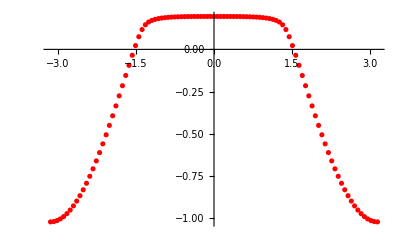

```mathematica
LandauLevelMixed1 = {};
Do[LandauLevelMixed1 = Append[LandauLevelMixed1,bb[[A -2+ n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed1,PlotStyle->Red]]
```

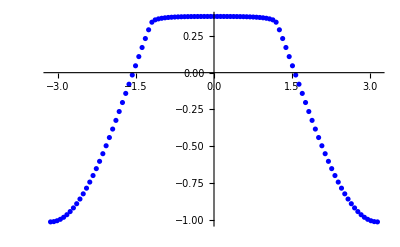

```mathematica
LandauLevelMixed2 = {};
Do[LandauLevelMixed2 = Append[LandauLevelMixed2,bb[[A + n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed2,PlotStyle->Blue]]
```

```mathematica
(** Here we plot the bandstructure, with the Landau levels shown explicitly **)
```

```mathematica
Show[Plot1,ListPlot[LandauLevelMixed1,PlotStyle->Red],ListPlot[LandauLevelMixed2,PlotStyle->Blue],ImageSize-> 800,FrameStyle-> Black]
```

-Graphics-

```mathematica
(** Export the above band structure **)
```

```mathematica
(** Export["WholeCrystalLandauLevels32x32.dat",bb] **)
```

```mathematica
tStop=AbsoluteTime[];
```

```mathematica
totalTimeInSeconds=tStop-tStart
```

1212.99919